y direction

## zero order

### Expressions set up

#### vE

```mathematica
Qy0=0;
Qy1=bmu^2+(bmu^2 BesselI[1,bJ])/BesselI[0,bJ];
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qy0-bmu(Sin[theta1]+Sin[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2+Qy0 bmu(Sin[theta1]+Sin[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

### Import

#### hns

Hns

```mathematica
H0y=Flatten[Import["~/Dropbox/Export/Y/H0y.xls"],1];
Table[H0[0,j_,xi_]:=ToExpression[H0y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H0cy=Flatten[Import["~/Dropbox/Export/Y/H0cy.xls"],1];
Table[H0c[n_,j_,xi_]:=ToExpression[H0cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H0sy=Flatten[Import["~/Dropbox/Export/Y/H0sy.xls"],1];
Table[H0s[n_,j_,xi_]:=ToExpression[H0sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

Ins

#### Ins

```mathematica
I0cchy=Flatten[Import["~/Dropbox/Export/Y/I0cchy.xls"],1];
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0schy=Flatten[Import["~/Dropbox/Export/Y/I0schy.xls"],1];
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0cshy=Flatten[Import["~/Dropbox/Export/Y/I0cshy.xls"],1];
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0sshy=Flatten[Import["~/Dropbox/Export/Y/I0sshy.xls"],1];
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### Fns and Ens

```mathematica
F0sy=Flatten[Import["~/Dropbox/Export/Y/F0sy.xls"],1];
Table[F0s[n_,j_]:=ToExpression[F0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F0cy=Flatten[Import["~/Dropbox/Export/Y/F0cy.xls"],1];
Table[F0c[n_,j_]:=ToExpression[F0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0sy=Flatten[Import["~/Dropbox/Export/Y/E0sy.xls"],1];
Table[E0s[n_,j_]:=ToExpression[E0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0cy=Flatten[Import["~/Dropbox/Export/Y/E0cy.xls"],1];
Table[E0c[n_,j_]:=ToExpression[E0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### Ans

```mathematica
A0cy0=Flatten[Import["~/Dropbox/Export/Y/A0cy0.xls"],1];
A0cy=Flatten[Import["~/Dropbox/Export/Y/A0cy.xls"],1];
Table[A0c[0,j_,theta1_]:=ToExpression[A0cy0[[j+1,2]]],{j,0,10}];  
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A0sy=Flatten[Import["~/Dropbox/Export/Y/A0sy.xls"],1];
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0cy0=Flatten[Import["~/Dropbox/Export/Y/dA0cy0.xls"],1];
dA0cy=Flatten[Import["~/Dropbox/Export/Y/dA0cy.xls"],1];
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cy0[[j+1,2]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0sy=Flatten[Import["~/Dropbox/Export/Y/dA0sy.xls"],1];
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

### A0ns and dA0ns summing j

```mathematica
Ayc0[n_,theta1_]:=1/(bJ+4 bJ n^4)(2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[n theta1] Sin[theta1]-2 bmu n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Cos[theta1] Sin[n theta1])
Ayc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
dAyc0[n_,theta1_]:=1/(bJ+4 bJ n^4)2 bmu ((bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Sin[theta1] Sin[n theta1])
dAyc0[0,theta1_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Cos[theta1]
```

```mathematica
Ays0[n_,theta1_]:=1/(bJ+4 bJ n^4)bmu (bJ (1+2 (-1+n) n) BesselI[1+n,bJ] (-Cos[theta1+n theta1]+Cosh[n theta1])+bJ BesselI[-1+n,bJ] ((1+2 n (1+n)) Cos[(-1+n) theta1]+(-1-2 (-1+n) n) Cosh[n theta1])+2 BesselI[n,bJ] (2 bJ n Cos[theta1] Cos[n theta1]+n (1+2 (-1+n) n) Cosh[n theta1]+bJ (1+2 n^2) Sin[theta1] Sin[n theta1]))
Ays0[0,theta1_]:=0
```

```mathematica
dAys0[n_,theta1_]:=1/(1+4 n^4)bmu ((1+n-2 n^3) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (n (-1+2 n^2) Cos[n theta1] Sin[theta1]+Cos[theta1] Sin[n theta1])+(1-n+2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAys0[0,theta1_]:=0
```

### test for Hns

#### H0

```mathematica
(*H0nNumerical[bJ_,bmu_,theta1_]:=NIntegrate[Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/2/Pi*)
```

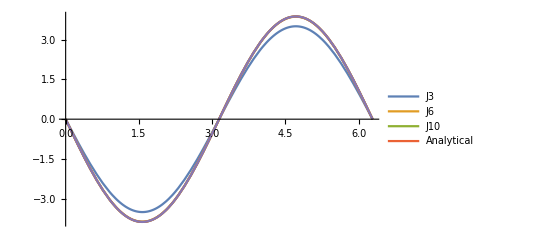

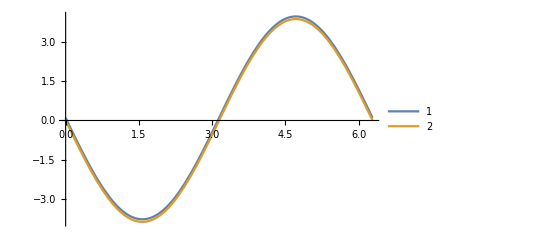

```mathematica
(*bmu=1;bJ=2;
t13=Sum[H0[0,j,theta1],{j,0,3}];
t16=Sum[H0[0,j,theta1],{j,0,6}];
t110=Sum[H0[0,j,theta1],{j,0,10}];
analytical=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1];
Plot[{t13,t16,t110,analytical,H0nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"J3","J6","J10","Analytical"}]
Plot[{analytical*1.05,H0nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"1","2"}]*)
```

```mathematica
(**)
```

#### H0c

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 8.46083 ,bJ= 6.92378

```mathematica
(*HncNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Cos[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/Pi
a[n_]:=-bmu (2 BesselI[n,bJ] Cos[n theta1] Sin[theta1]-BesselI[-1+n,bJ] Sin[(-1+n) theta1]+BesselI[1+n,bJ] Sin[(1+n) theta1])*)
```

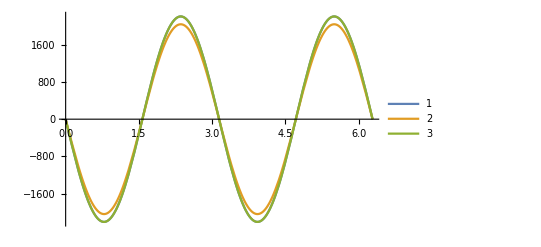

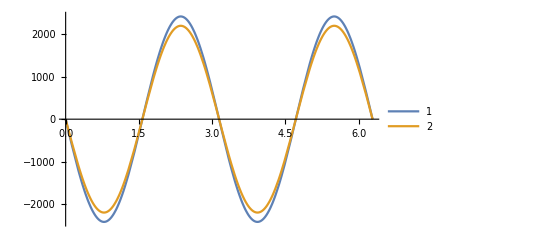

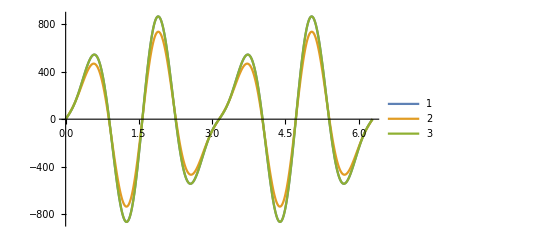

```mathematica
(*series[n_]:=Sum[H0c[n,j,theta1],{j,0,10}]
Plot[{a[1],series[1],HncNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[1]*1.1,HncNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[5],series[5],HncNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### H0s

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 0.825604 ,bJ= 1.3248

```mathematica
(*HnsNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Sin[n theta2]Exp[bJ Cos[theta1-theta2]] (0-bmu(Sin[theta1]+Sin[theta2])),{theta2,0,2Pi}]/Pi*)
```

```mathematica
(*a[n_]:=-bmu (BesselI[-1+n,bJ] Cos[(-1+n) theta1]-BesselI[1+n,bJ] Cos[(1+n) theta1]+2 BesselI[n,bJ] Sin[theta1] Sin[n theta1])
series[n_]:=Sum[H0s[n,j,theta1],{j,0,10}];*)
```

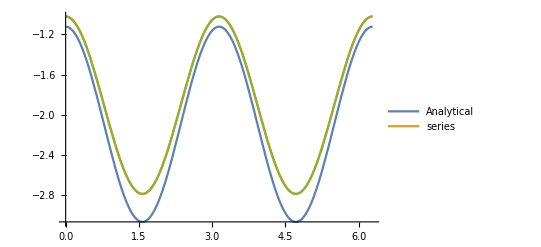

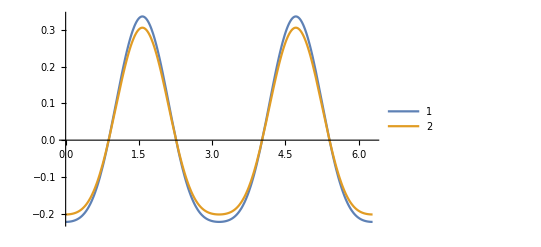

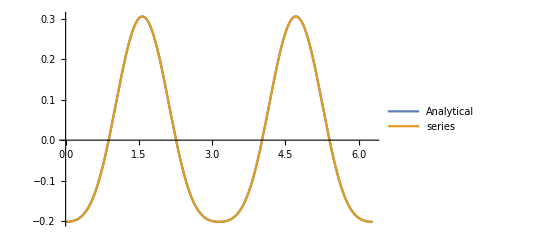

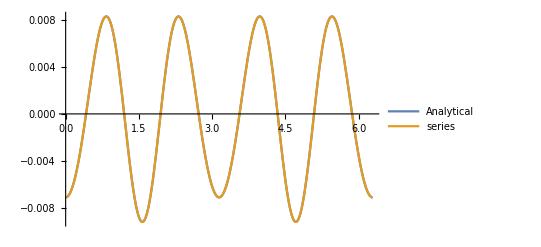

```mathematica
(*
Plot[{a[1]*1.1,series[1],HnsNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
Plot[{a[3]*1.1,HnsNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{a[3],series[3]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
Plot[{a[5],series[5]},{theta1,0,2Pi},PlotLegends->{"Analytical","series"}]
*)
```

```mathematica
(**)
```

### test for F0ns and E0ns

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 5.39774 ,bJ= 7.28836

```mathematica
(*F0cn[n_]:=1/n^2 bmu (BesselI[1+n,bJ] Sin[(1+n) theta1]+BesselI[-1+n,bJ] Sin[theta1-n theta1]);*)
```

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];*)
```

value start to change for bJ get biggers

```mathematica
(*E0sn[n_]:=1/(bJ+4 bJ n^4)2 bmu (-BesselI[n,bJ]+(-1+2 n^2) (bJ BesselI[-1+n,bJ]+(bJ-n) BesselI[n,bJ]))*)
```

does not agree!!

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Sum[E0s[1,j],{j,0,10}]//N
E0sn[1]//N
Sum[E0s[3,j],{j,0,10}]//N
E0sn[3]//N
Sum[E0s[5,j],{j,0,10}]//N
E0sn[5]//N*)
```

bmu = 8.03967 ,bJ= 4.98876

0.

133.128

0.

17.8808

0.

1.58302

```mathematica
(*Table[E0c[n,j],{n,1,5},{j,0,10}]*)
```

{{0.,8.02159,10.0044,24.9548,20.7489,25.8779,16.1373,13.4175,6.69366,4.17413,1.73531},{0.,-2.0054,0.384786,-3.83921,0.798036,-2.73708,0.620665,-1.03212,0.257449,-0.240815,0.0667427},{0.,0.,-1.28262,0.0426579,-1.96849,0.0663535,-1.20823,0.0412846,-0.411918,0.0142705,-0.0902616},{0.,0.,0.,-0.623871,0.0063259,-0.77318,0.00787185,-0.399252,0.0040815,-0.117807,0.00120928},{0.,0.,0.,0.,-0.253036,0.0010347,-0.261965,0.00107297,-0.116232,0.000476853,-0.0300832}}

### test for A0ns

#### A0 and dA0

4

bmu = 8.81937 ,bJ= 4

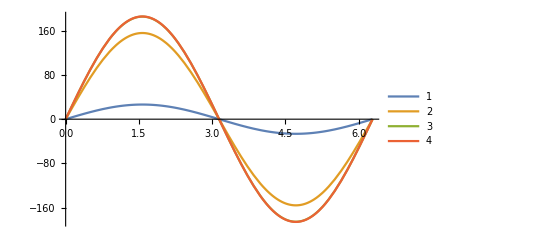

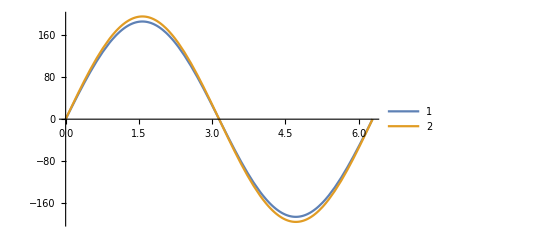

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
bJ=4
Print["bmu = ",bmu," ,bJ= " , bJ]
A0=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1];
s1=Sum[A0c[0,j,theta1],{j,0,1}];
s5=Sum[A0c[0,j,theta1],{j,0,5}];
s10=Sum[A0c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,A0},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s10,A0*1.05},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

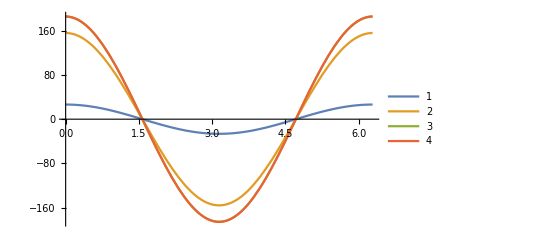

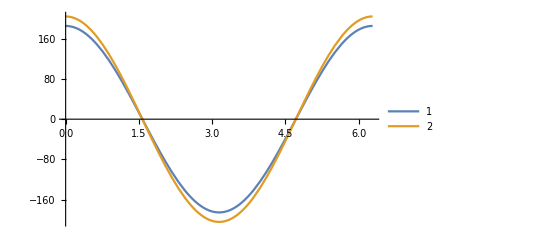

```mathematica
(*dA0=bmu (BesselI[0,bJ]+BesselI[1,bJ]) Cos[theta1];
s1=Sum[dA0c[0,j,theta1],{j,0,1}];
s5=Sum[dA0c[0,j,theta1],{j,0,5}];
s10=Sum[dA0c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,dA0},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s10,dA0*1.1},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### Acyn and dAcyn

bmu = 4.50623 ,bJ= 2.84058

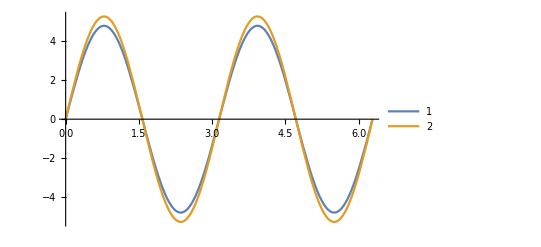

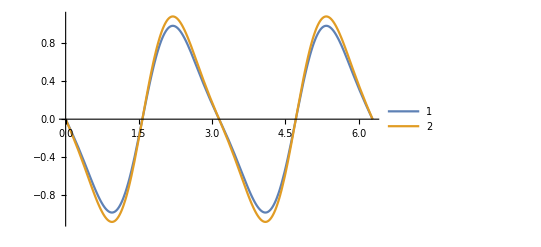

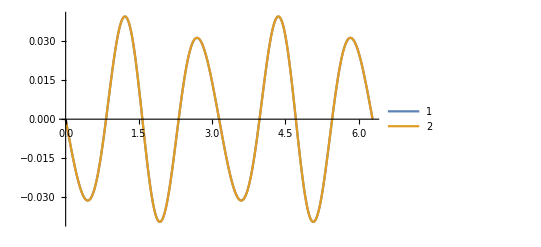

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
Acyn[n_]:=1/(bJ+4 bJ n^4)(2 bmu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[n theta1] Sin[theta1]-2 bmu n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Cos[theta1] Sin[n theta1])
s1=Sum[A0c[1,j,theta1],{j,0,10}];
s3=Sum[A0c[3,j,theta1],{j,0,10}];
s5=Sum[A0c[5,j,theta1],{j,0,10}];
Plot[{s1,Acyn[1]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,Acyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,Acyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

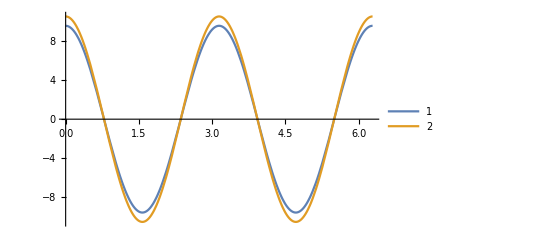

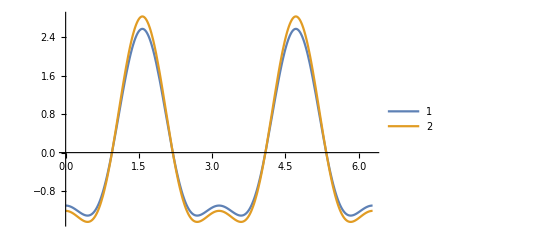

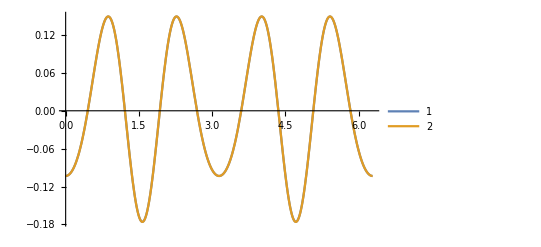

```mathematica
(*dAcyn[n_]:=1/(bJ+4 bJ n^4)2 bmu ((bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Sin[theta1] Sin[n theta1])
s1=Sum[dA0c[1,j,theta1],{j,0,10}];
s3=Sum[dA0c[3,j,theta1],{j,0,10}];
s5=Sum[dA0c[5,j,theta1],{j,0,10}];
Plot[{s1,dAcyn[1]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,dAcyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,dAcyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### Asyn and dAsyn

```mathematica
(*bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]*)
```

bmu = 6.67141 ,bJ= 2.54098

bmu = 7.76812 ,bJ= 9.96445

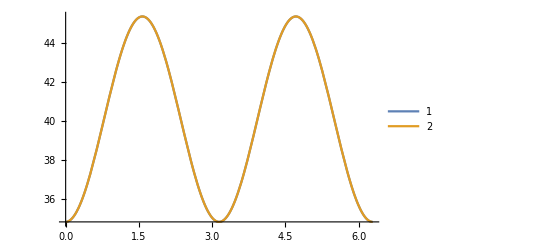

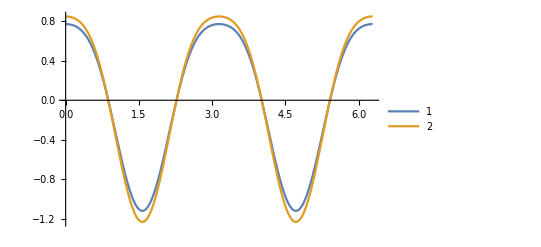

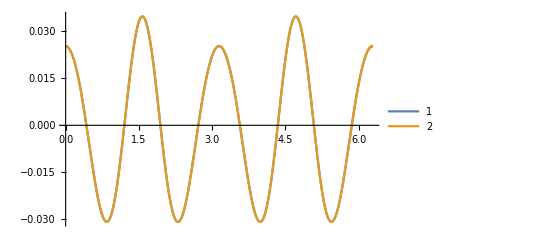

```mathematica
(*Asyn[n_]:=1/(bJ+4 bJ n^4)bmu (bJ (1+2 (-1+n) n) BesselI[1+n,bJ] (-Cos[theta1+n theta1]+Cosh[n theta1])+bJ BesselI[-1+n,bJ] ((1+2 n (1+n)) Cos[(-1+n) theta1]+(-1-2 (-1+n) n) Cosh[n theta1])+2 BesselI[n,bJ] (2 bJ n Cos[theta1] Cos[n theta1]+n (1+2 (-1+n) n) Cosh[n theta1]+bJ (1+2 n^2) Sin[theta1] Sin[n theta1]))
s1=Sum[A0s[1,j,theta1],{j,0,10}];
s3=Sum[A0s[3,j,theta1],{j,0,10}];
s5=Sum[A0s[5,j,theta1],{j,0,10}];
Plot[{s1,Asyn[1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,Asyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,Asyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

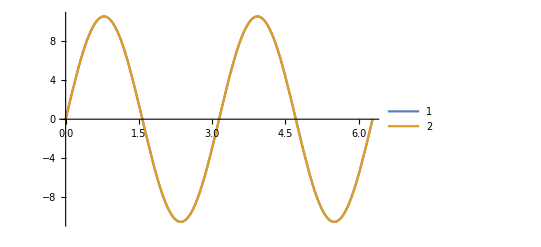

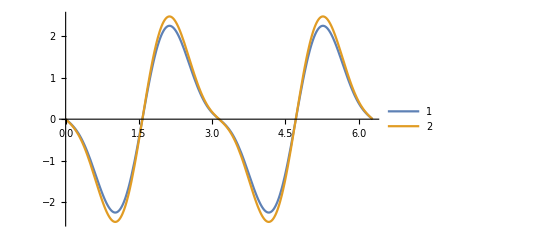

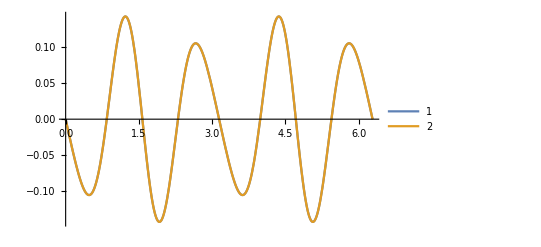

```mathematica
(*dAsyn[n_]:=1/(1+4 n^4)bmu ((1+n-2 n^3) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (n (-1+2 n^2) Cos[n theta1] Sin[theta1]+Cos[theta1] Sin[n theta1])+(1-n+2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
s1=Sum[dA0s[1,j,theta1],{j,0,10}];
s3=Sum[dA0s[3,j,theta1],{j,0,10}];
s5=Sum[dA0s[5,j,theta1],{j,0,10}];
Plot[{s1,dAsyn[1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s3,dAsyn[3]*1.1},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{s5,dAsyn[5]},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

### test for pv0ns

```mathematica
pvy10[theta1_,theta2_,nmax_]:=Sum[dAys0[n,theta1]Sin[n theta2]+dAyc0[n,theta1]Cos[n theta2],{n,0,nmax}]
pvy20[theta1_,theta2_,nmax_]:=Sum[n Ays0[n,theta1]Cos[n theta2]-n Ayc0[n,theta1]Sin[n theta2],{n,1,nmax}]
pvy10n[theta1_,theta2_,nmax_]:=dAys0[n,theta1]Sin[n theta2]+dAyc0[n,theta1]Cos[n theta2]
pvy20n[theta1_,theta2_,nmax_]:=n Ays0[n,theta1]Cos[n theta2]-n Ayc0[n,theta1]Sin[n theta2]
```

2

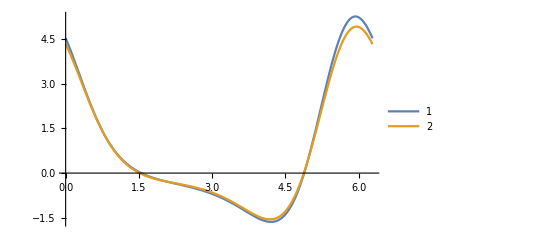

```mathematica
myt2=RandomReal[{0,2Pi}];
bJ=1.0;
bmu=1.0;
nmax=2
Plot[{pvy10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

2.20592

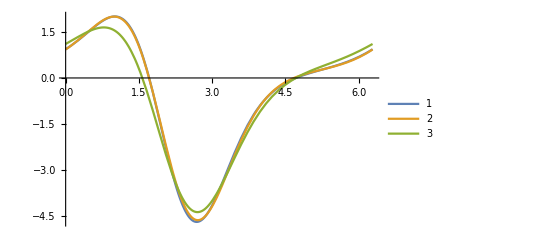

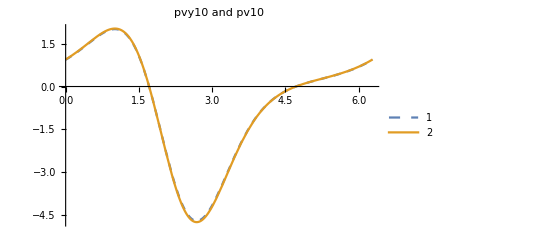

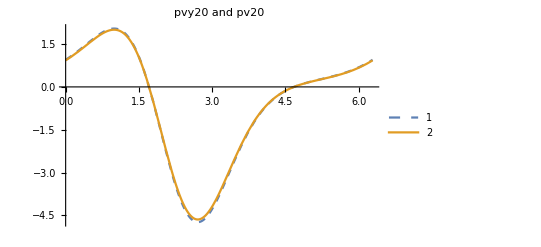

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=2;
jmax=10;
Plot[{pvy10[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]],pv10[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
Plot[{pvy10[ theta1,myt2,nmax]Exp[Cos[theta1-myt2]],pv10[1.0,1.0,theta1,myt2]Exp[Cos[theta1-myt2]]*1.01},{theta1,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvy10 and pv10"]
Plot[{pvy20[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]*1.02,pv20[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick},PlotLegends->Automatic,PlotLabel->"pvy20 and pv20"]
```

## First order

### Set up

#### vEE

```mathematica
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

small question here, I1CCH integrate along theta1?

```mathematica
F1s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1sch[n,j,2Pi]+1/(2n)I1ssh[n,j,2Pi]
F1c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1cch[n,j,2Pi]+1/(2n)I1csh[n,j,2Pi]
E1s[n_,j_]:=F1s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1ssh[n,j,2Pi]
E1c[n_,j_]:=F1c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1csh[n,j,2Pi]
```

```mathematica
A1c[0,j_,theta1_]:=Integrate[H1[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A1s[0,j_,theta1_]:=0
A1s[n_,j_,theta1_]:=E1s[n,j]Sinh[n theta1]+F1s[n,j]Cosh[n theta1]+1/n I1ssh[n,j,theta1]
A1c[n_,j_,theta1_]:=E1c[n,j]Sinh[n theta1]+F1c[n,j]Cosh[n theta1]+1/n I1csh[n,j,theta1]
dA1c[0,j_,theta1_]:=Integrate[H1[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA1s[0,j_,theta1_]:=0
dA1s[n_,j_,theta1_]:=n E1s[n,j]Cosh[n theta1]+n F1s[n,j]Sinh[n theta1]+I1sch[n,j,theta1]
dA1c[n_,j_,theta1_]:=n E1c[n,j]Cosh[n theta1]+n F1c[n,j]Sinh[n theta1]+I1cch[n,j,theta1]
```

### Import

```mathematica
(*Export["~/Dropbox/Export/Y/H1yMore.xls",Table[{j,H1[0,j,theta1]},{j,0,20}]//Simplify];*)
Timing[%]
```

{0.000011,Null}

```mathematica
(*H1y=Flatten[Import["~/Dropbox/Export/Y/H1yMore.xls"],1];
Table[H1[0,j_,xi_]:=ToExpression[H1y[[j+1,2]]]/.theta1->xi,{j,0,20}];*)
```

```mathematica
H1y=Flatten[Import["~/Dropbox/Export/Y/H1y.xls"],1];
Table[H1[0,j_,xi_]:=ToExpression[H1y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H1cy=Flatten[Import["~/Dropbox/Export/Y/H1cy.xls"],1];
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H1sy=Flatten[Import["~/Dropbox/Export/Y/H1sy.xls"],1];
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cchy=Flatten[Import["~/Dropbox/Export/Y/I1cchy.xls"],1];
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1schy=Flatten[Import["~/Dropbox/Export/Y/I1schy.xls"],1];
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cshy=Flatten[Import["~/Dropbox/Export/Y/I1cshy.xls"],1];
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1sshy=Flatten[Import["~/Dropbox/Export/Y/I1sshy.xls"],1];
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
F1sy=Flatten[Import["~/Dropbox/Export/Y/F1sy.xls"],1];
Table[F1s[n_,j_]:=ToExpression[F1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F1cy=Flatten[Import["~/Dropbox/Export/Y/F1cy.xls"],1];
Table[F1c[n_,j_]:=ToExpression[F1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1sy=Flatten[Import["~/Dropbox/Export/Y/E1sy.xls"],1];
Table[E1s[n_,j_]:=ToExpression[E1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1cy=Flatten[Import["~/Dropbox/Export/Y/E1cy.xls"],1];
Table[E1c[n_,j_]:=ToExpression[E1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1cy0=Flatten[Import["~/Dropbox/Export/Y/A1cy0.xls"],1];
A1cy=Flatten[Import["~/Dropbox/Export/Y/A1cy.xls"],1];
```

```mathematica
Table[A1c[0,j_,theta1_]:=ToExpression[A1cy0[[j+1,2]]],{j,0,10}];
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1sy=Flatten[Import["~/Dropbox/Export/Y/A1sy.xls"],1];
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1cy0=Flatten[Import["~/Dropbox/Export/Y/dA1cy0.xls"],1];
dA1cy=Flatten[Import["~/Dropbox/Export/Y/dA1cy.xls"],1];
```

```mathematica
Table[dA1c[0,j_,theta1_]:=ToExpression[dA1cy0[[j+1,2]]],{j,0,10}];
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1sy=Flatten[Import["~/Dropbox/Export/Y/dA1sy.xls"],1];
dA1s[0,j,theta1]:=0;
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
Qy1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ];
```

### A1ns and dA1ns summing j

```mathematica
Ayc1[0,theta1_]:=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2
```

```mathematica
Ayc1[n_,theta1_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] (-Cos[(-2+n) theta1]+Cosh[n theta1]))/(2+(-2+n) n)-(4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1])))/(bJ^2 (4+n^4) BesselI[0,bJ]))
```

```mathematica
dAyc1[n_,theta1_]:=1/4 bmu^2 (((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))
```

```mathematica
dAyc1[0,theta1_]:=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1]
```

```mathematica
Ays1[n_,theta1_]:=(bmu^2 (-bJ n^2 (2+n (2+n)) BesselI[0,bJ] ((-1+bJ+n) BesselI[-1+n,bJ]+bJ BesselI[n,bJ]) Sin[(-2+n) theta1]-2 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1]-n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))/(2 bJ^2 n^2 (4+n^4) BesselI[0,bJ])
```

```mathematica
dAys1[n_,theta1_]:=1/4 bmu^2 (-((-2+n) BesselI[-2+n,bJ] Cos[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Cos[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]))
```

```mathematica
Ays1[0,theta1_]:=0
dAys1[0,theta1_]:=0
```

### test for Hns

#### H1

```mathematica
H1nNumerical[bJ_,bmu_,theta1_]:=NIntegrate[Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/2/Pi
```

1/2 (BesselI[0,2]+2 BesselI[1,2]+BesselI[2,2]) Cos[2 theta1]

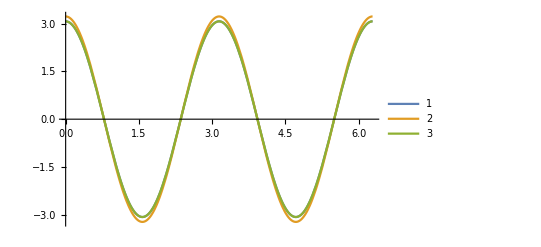

```mathematica
bmu=1;bJ=2;
t2=1/2 (BesselI[0,2]+2 BesselI[1,2]+BesselI[2,2]) Cos[2 theta1]
Plot[{t2,t2*1.05,H1nNumerical[bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

#### H1c

```mathematica
H1nCNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Cos[n theta2]*Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/Pi
```

```mathematica
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
```

bmu = 0.416893 ,bJ= 2.59718

```mathematica
A[n_]:=1/(2 BesselI[0,bJ])bmu^2 (4 BesselI[1,bJ] BesselI[n,bJ] Cos[n theta1]+BesselI[0,bJ] (BesselI[-2+n,bJ] Cos[(-2+n) theta1]+2 BesselI[n,bJ] Cos[2 theta1] Cos[n theta1]+BesselI[2+n,bJ] Cos[(2+n) theta1]+4 BesselI[-1+n,bJ] Sin[theta1] Sin[(-1+n) theta1]-4 BesselI[1+n,bJ] Sin[theta1] Sin[(1+n) theta1]))
```

```mathematica
t1=Sum[H1c[1,j,theta1],{j,0,10}];
t3=Sum[H1c[3,j,theta1],{j,0,10}];
t5=Sum[H1c[5,j,theta1],{j,0,10}];
```

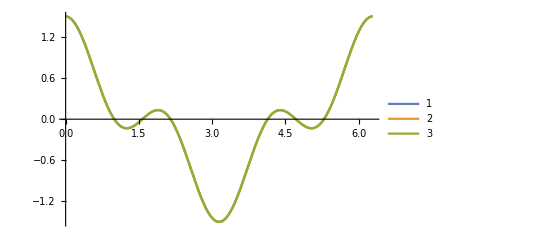

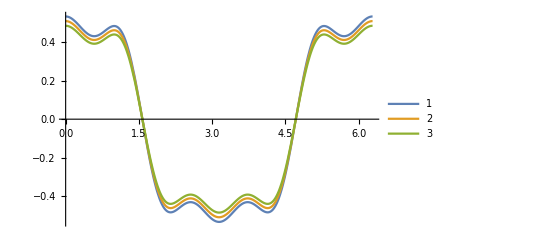

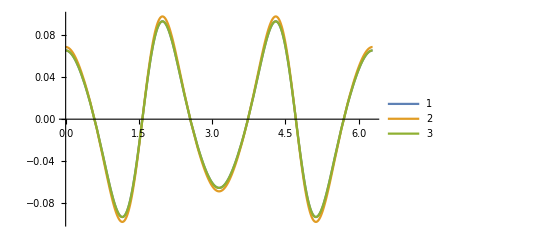

```mathematica
Plot[{t1,A[1],H1nCNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{t3*1.10,A[3]*1.05,H1nCNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{t5,A[5]*1.05,H1nCNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

#### H1s

```mathematica
bmu=RandomReal[{0.001,10}];
bJ=RandomReal[{0.001,10}];
Print["bmu = ",bmu," ,bJ= " , bJ]
```

bmu = 7.10784 ,bJ= 4.53077

```mathematica
H1nsNumerical[n_,bJ_,bmu_,theta1_]:=NIntegrate[Sin[n theta2]*Exp[bJ Cos[theta1-theta2]] (Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2),{theta2,0,2Pi}]/Pi
```

```mathematica
A[n_]:=1/(2 BesselI[0,bJ])bmu^2 (4 BesselI[1,bJ] BesselI[n,bJ] Sin[n theta1]+BesselI[0,bJ] (-4 BesselI[-1+n,bJ] Cos[(-1+n) theta1] Sin[theta1]+4 BesselI[1+n,bJ] Cos[(1+n) theta1] Sin[theta1]+BesselI[-2+n,bJ] Sin[(-2+n) theta1]+2 BesselI[n,bJ] Sin[n theta1]-4 BesselI[n,bJ] Sin[theta1]^2 Sin[n theta1]+BesselI[2+n,bJ] Sin[(2+n) theta1]));
```

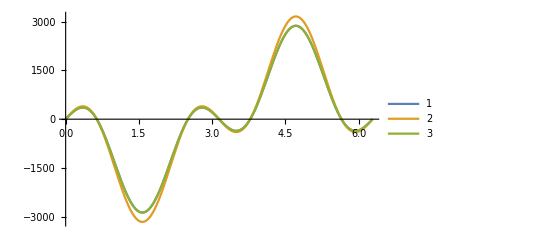

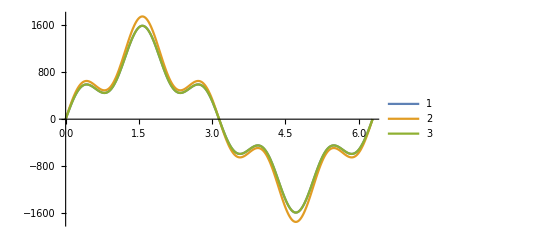

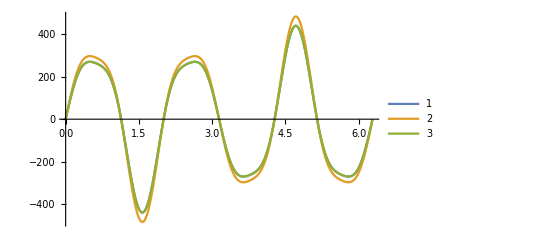

```mathematica
Plot[{A[1],A[1]*1.1,H1nsNumerical[1,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{A[3],A[3]*1.1,H1nsNumerical[3,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
Plot[{A[5],A[5]*1.1,H1nsNumerical[5,bJ,bmu,theta1]},{theta1,0,2Pi},PlotLegends->Automatic]
```

### test for A1ns

#### A1cyn0 and dA1cyn0

9.59048

3.0768

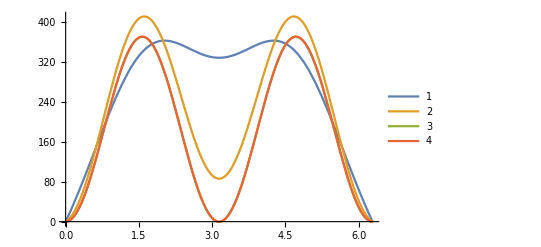

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]
A1cyn0=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[theta1]^2;
s1=Sum[A1c[0,j,theta1],{j,0,1}];
s5=Sum[A1c[0,j,theta1],{j,0,5}];
s10=Sum[A1c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,A1cyn0},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

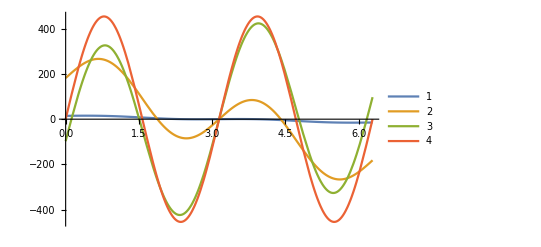

```mathematica
(*dA1cyn0=1/4 bmu^2 (BesselI[0,bJ]+2 BesselI[1,bJ]+BesselI[2,bJ]) Sin[2 theta1];
s1=Sum[dA1c[0,j,theta1],{j,0,1}];
s5=Sum[dA1c[0,j,theta1],{j,0,5}];
s10=Sum[dA1c[0,j,theta1],{j,0,10}];
Plot[{s1,s5,s10,dA1cyn0},{theta1,0,2Pi},PlotLegends->Automatic]*)
```

#### A1cyn and dA1cyn

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]*)
```

2.62901

7.83994

```mathematica
(*A1cyn[n_]:=1/(4 n^2)bmu^2 ((n^2 BesselI[-2+n,bJ] (-Cos[(-2+n) theta1]+Cosh[n theta1]))/(2+(-2+n) n)-(4 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1]+2 n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]+bJ n^2 (2+n (2+n)) BesselI[0,bJ] (bJ BesselI[n,bJ] (Cos[(-2+n) theta1]+Cosh[n theta1])+2 BesselI[-1+n,bJ] (bJ Cos[(-2+n) theta1]+(-1+n) Cosh[n theta1])))/(bJ^2 (4+n^4) BesselI[0,bJ]))*)
```

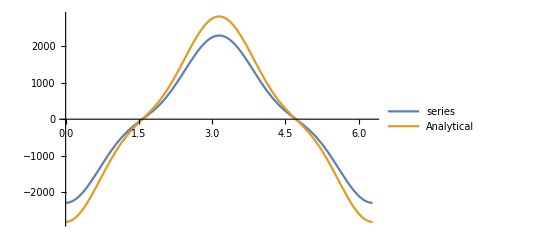

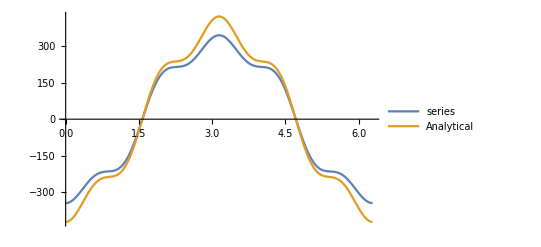

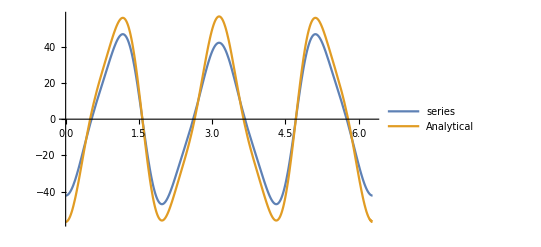

```mathematica
(*Plot[{Sum[A1c[1,j,theta1],{j,0,10}],A1cyn[1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[3,j,theta1],{j,0,10}],A1cyn[3]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1c[5,j,theta1],{j,0,10}],A1cyn[5]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
*)
```

```mathematica
(*dA1cyn[n_]:=1/4 bmu^2 (((-2+n) BesselI[-2+n,bJ] Sin[(-2+n) theta1])/(2+(-2+n) n)+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Sin[(-2+n) theta1]+4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1])+2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))*)
```

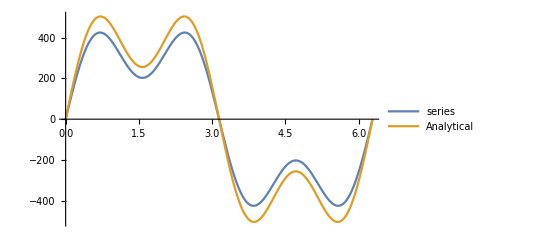

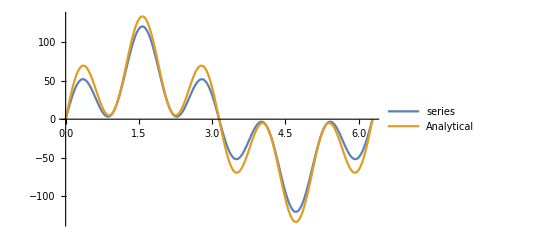

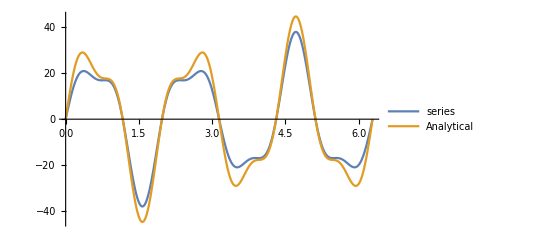

```mathematica
(*Plot[{Sum[dA1c[1,j,theta1],{j,0,10}],dA1cyn[1]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[3,j,theta1],{j,0,10}],dA1cyn[3]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1c[5,j,theta1],{j,0,10}],dA1cyn[5]},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

#### A1syn and dA1syn

```mathematica
(*bmu=RandomReal[{1,10}]
bJ=RandomReal[{1,10}]*)
```

1.27432

7.65271

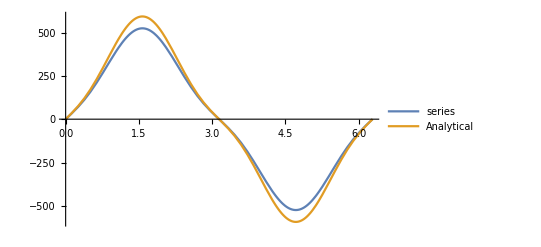

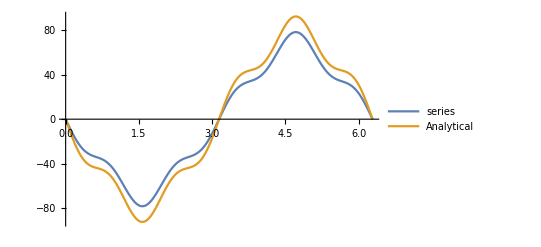

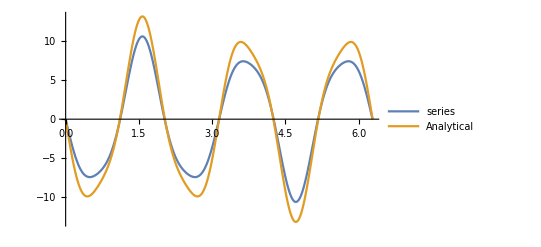

```mathematica
(*A1syn[n_]:=(bmu^2 (-bJ n^2 (2+n (2+n)) BesselI[0,bJ] ((-1+bJ+n) BesselI[-1+n,bJ]+bJ BesselI[n,bJ]) Sin[(-2+n) theta1]-2 bJ (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Sin[n theta1]-n^2 (2+(-2+n) n) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Sin[(2+n) theta1]))/(2 bJ^2 n^2 (4+n^4) BesselI[0,bJ])
Plot[{Sum[A1s[1,j,theta1],{j,0,10}],A1syn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[3,j,theta1],{j,0,10}],A1syn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[A1s[5,j,theta1],{j,0,10}],A1syn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

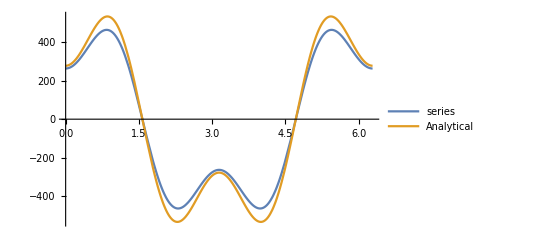

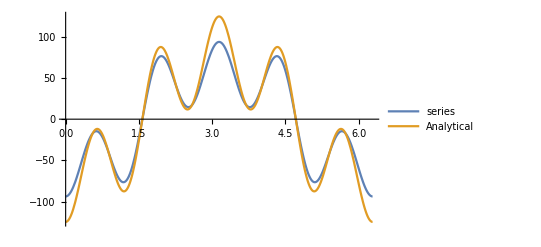

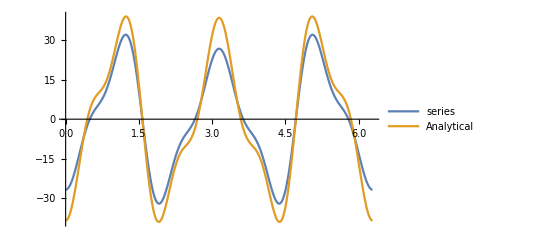

```mathematica
(*dA1syn[n_]:=1/4 bmu^2 (-(((-2+n) BesselI[-2+n,bJ] Cos[(-2+n) theta1])/(2+(-2+n) n))+1/(bJ^2 n (4+n^4) BesselI[0,bJ])(bJ (-bJ n (-4-2 n+n^3) BesselI[0,bJ] (2 BesselI[-1+n,bJ]+BesselI[n,bJ]) Cos[(-2+n) theta1]-4 (4+n^4) (bJ BesselI[1,bJ] BesselI[n,bJ]+BesselI[0,bJ] (-bJ BesselI[-1+n,bJ]+n BesselI[n,bJ])) Cos[n theta1])-2 n (4-2 n+n^3) BesselI[0,bJ] (bJ (-1+bJ-n) BesselI[-1+n,bJ]+(bJ^2-2 bJ n+2 n (1+n)) BesselI[n,bJ]) Cos[(2+n) theta1]));
Plot[{Sum[dA1s[1,j,theta1],{j,0,10}],dA1syn[1]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1s[3,j,theta1],{j,0,10}],dA1syn[3]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]
Plot[{Sum[dA1s[5,j,theta1],{j,0,10}],dA1syn[5]*1.05},{theta1,0,2Pi},PlotLegends->{"series","Analytical"}]*)
```

### test for pv1ns

```mathematica
pv11[bJx_,bmux_,xi_,xj_]:=Release[Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]]
pv21[bJx_,bmux_,xi_,xj_]:=Release[Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]]
```

```mathematica
pvy11[theta1_,theta2_,nmax_]:=Sum[dAys1[n,theta1]Sin[n theta2]+dAyc1[n,theta1]Cos[n theta2],{n,0,nmax}]
pvy21[theta1_,theta2_,nmax_]:=Sum[n Ays1[n,theta1]Cos[n theta2]-n Ayc1[n,theta1]Sin[n theta2],{n,1,nmax}]
pvy11n[theta1_,theta2_,nmax_]:=dAys1[n,theta1]Sin[n theta2]+dAyc1[n,theta1]Cos[n theta2]
pvy21n[theta1_,theta2_,nmax_]:=n Ays1[n,theta1]Cos[n theta2]-n Ayc1[n,theta1]Sin[n theta2]
```

1.98734

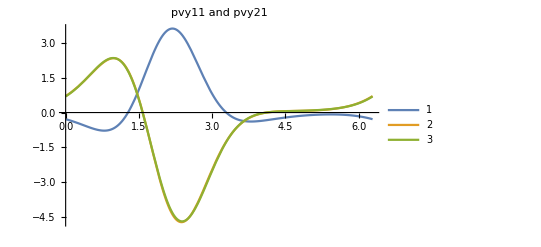

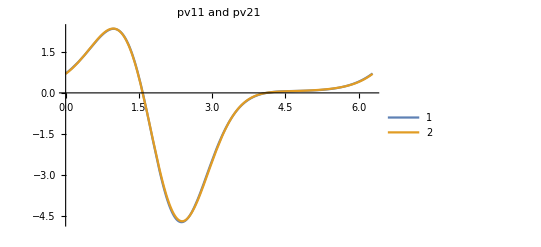

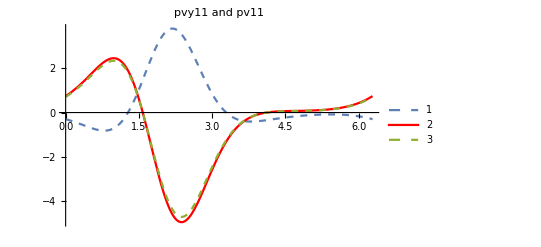

```mathematica
myt2=RandomReal[{0,2Pi}]
bJ=1.0;
bmu=1.0;
nmax=RandomInteger[{1,3}];
nmax=3;
jmax=10;
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]],pvy21[ myt2,theta2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvy11 and pvy21"]
Plot[{pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]],pv21[1.0,1.0,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pv11 and pv21"]
Plot[{pvx11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pvy11[ theta2,myt2,nmax]Exp[Cos[theta2-myt2]]*1.05,pv11[1.0,1.0,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic,PlotLabel->"pvy11 and pv11",PlotStyle->{Dashed,Red}]
```